```mathematica
s[t_]:=1/π σ/(t^2+σ^2) Sin[ω t]
Ν=1000;
σ=2.4;
ω=1;
sn[T_]:=Table[{t,s[t]},{t,-T/2.+T/(2 Ν),T/2-T/(2 Ν),T/Ν}]
```

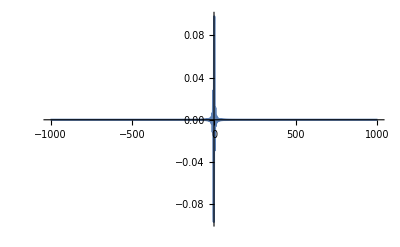

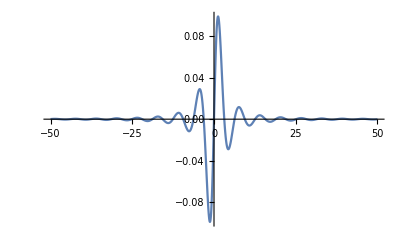

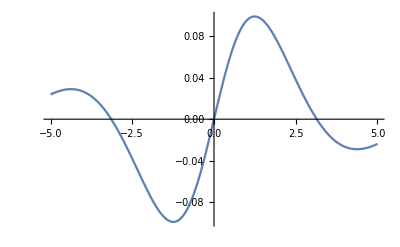

```mathematica
Plot[s[t],{t,-1000,1000},PlotRange->All]
Plot[s[t],{t,-50,50},PlotRange->All]
Plot[s[t],{t,-5,5},PlotRange->All]
```

```mathematica
fs[ν_]=FourierTransform[s[t],t,ν,FourierParameters->{0,-2 Pi}];
absfs[ν_]=Abs[fs[ν]]^2;
```

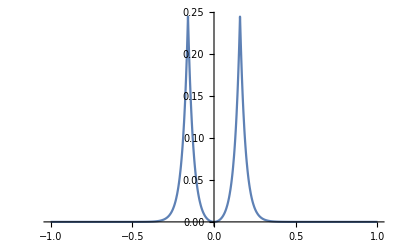

```mathematica
Plot[absfs[ν],{ν,-1,1},PlotRange->All]
```

```mathematica
fsn[T_]:=Table[{z/T,1/(√Ν) Total[(#[[2]]&/@sn[T]) Array[ⅇ^(-ⅈ 2 π z #/Ν)&,Ν,{1.,Ν}]]},{z,-Ν/2.+1,Ν/2}]
absfsn[T_]:={#[[1]],Abs[#[[2]]]^2}&/@fsn[T]
```

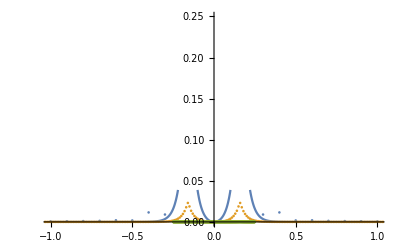

```mathematica
Show[Plot[absfs[ν],{ν,-1,1},PlotPoints->100],ListPlot[{absfsn[10],absfsn[100],absfsn[2000]}],PlotRange->{{-1,1},{0,.25}}]
```